## Compare Health Insurance Plans

{{2180,0},{2180,0},{2180,0},{2180,0},{160,0},{160,0},{160,0},{160,0},{160,2250},{160,2250},{160,2250},{160,2250},{160,2250},{160,2250},{160,2250},{160,2250},{160,2250},{160,2250},{160,2250},{200,2250},{200,2250},{200,2250},{200,2250},{450,1000},{450,1000},{220,1000},{220,1000},{220,0},{220,0},{420,0},{420,0},{420,0}}

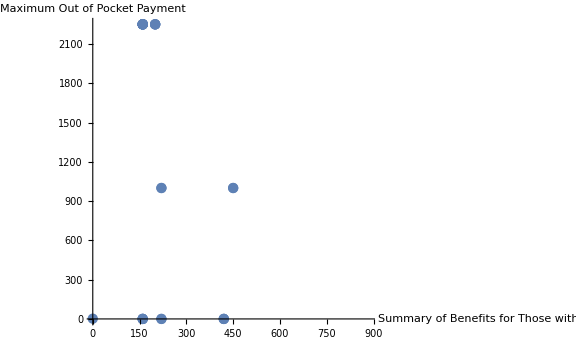

DeleteDuplicates::normal: Nonatomic expression expected at position 1 in DeleteDuplicates[data].

General::stop: Further output of DeleteDuplicates::normal will be suppressed during this calculation.

DeleteDuplicates::argb: DeleteDuplicates called with 0 arguments; between 1 and 3 arguments are expected.

General::stop: Further output of DeleteDuplicates::argb will be suppressed during this calculation.

-Graphics-

Select a metal level. The metal level indicates the ratio between how much you pay, and how much the insurance company pays. The higher the metal level, the higher the monthly payment and the lower the costs when you need healthcare.

Select your state

Would you like an individual or small group plan?

If you have a company in mind to buy from, select from the list below

Compare your options

```mathematica
hiData =Import["C:\\Users\\yuwer\\OneDrive\\Desktop\\Hackathon\\HexCambridge\\MoneyApp\\Data\\planAttributes.csv", "Data"];
gaData =Import["C:\\Users\\yuwer\\OneDrive\\Desktop\\Hackathon\\HexCambridge\\MoneyApp\\Data\\GAHI.csv", "Data"];

stateAbbrevData = DeleteDuplicates[ hiData[[All,136]]];
saDataSingleColumn = Sort[stateAbbrevData[[2;;39]]];



filterState = "Gold";
filterIndex = 104;

f2=Function[{entry},If[StringFreeQ[entry[[filterIndex]],filterState]==False, Position[gaData, entry], False ]];

filteredList=DeleteDuplicates[Map[f2,gaData]];

filterState = "Humana";
filterIndex = 117;

filteredList2 = DeleteDuplicates[Map[f2,gaData]];
filteredList12=Intersection[filteredList, filteredList2];
filteredListFinal = Rest[filteredList12];

cleanList = filteredListFinal//.{x_List}:>x;

m = Function[{index},If[True, Part[gaData, index], False]];


tData = Map[m, cleanList]//.{x_List}:>x;
tData127 = tData[[All,127]];
tData122 = tData[[All,122]];
tDataCombined = Join[{tData127, tData122}, 2];
coorList={};

moop = Function[{ent},nums = StringCases[ent,DigitCharacter......];nums2=StringCases[nums, DigitCharacter..]converted = ToExpression[nums2]
];

mehbd = Function[{entr}, 
nums = StringCases[entr,DigitCharacter......];nums2=StringCases[nums, DigitCharacter..]converted = ToExpression[nums2]
];

For[i=1,i≤Length[cleanList],i++,
AppendTo[coorList, {Map[mehbd,tData3[[i]]//.{x_List}:>x], Map[moop, tData127[[i]]]//.{x_List}:>x} ]];

finalCoorList = coorList//.{x_List}:>x
AppendTo[finalCoorList, {0, 2}];

ListPlot[finalCoorList, AxesLabel->{"Summary of Benefits for Those with Diabetes", "Maximum Out of Pocket Payment"}, ImageSize->Large]


(*cleanList is a list of indexes*)
(*tData is the list of entries in gaData associated with cleanList indexes*)



filterData[mPick_,sPick_,gPick_,cPick_]:=Module[{},
filterState = mPick;
filterIndex = 104;

f2=Function[{entry},If[StringFreeQ[entry[[filterIndex]],filterState]==False, Position[gaData, entry], False ]];

filteredList=DeleteDuplicates[Map[f2,gaData]];

filterState = cPick;
filterIndex = 117;

filteredList2 = DeleteDuplicates[Map[f2,gaData]];

filterState = sPick;
filterIndex =136;

filteredList3 = DeleteDuplicates[Map[f2,gaData]];


filterState = gPick;
filterIndex =101;

filteredList4=DeleteDuplicates[Map[f2,gaData]];

filteredList12=Intersection[filteredList, filteredList2];
filteredList123=Intersection[filteredList12, filteredList3];
filteredList1234=Intersection[filteredList123, filteredList4];
filteredListFinal = Rest[filteredList1234];

cleanList =filteredListFinal//.{x_List}:>x;

m = Function[{index},If[True, Part[gaData, index], False]];

(*Summary of Benefits for Copayment for those with Diabetes*)
tData = Map[m, cleanList]//.{x_List}:>x;
tData127 = tData[[All,127]];

(*Max out of pocket payment*)
tData122 = tData[[All,122]];
tDataCombined = Join[{tData127, tData122}, 2];
coorList={};

moop = Function[{ent},nums = StringCases[ent,DigitCharacter......];nums2=StringCases[nums, DigitCharacter..]converted = ToExpression[nums2]
];

mehbd = Function[{entr}, 
nums = StringCases[entr,DigitCharacter......];nums2=StringCases[nums, DigitCharacter..]converted = ToExpression[nums2]
];

For[i=1,i≤Length[cleanList],i++,
AppendTo[coorList, {Map[mehbd,tData3[[i]]//.{x_List}:>x], Map[moop, tData127[[i]]]//.{x_List}:>x} ]];

finalCoorList = coorList//.{x_List}:>x
AppendTo[finalCoorList, {0, 2}];

ListPlot[finalCoorList,AxesLabel->{"Summary of Benefits for Those with Diabetes", "Maximum Out of Pocket Payment"}, ImageSize->Large]];


filterData["Silver", "GA", "Individual", "Humana"]


mapData = Function[{filData}, 

];


Text["Select a metal level. The metal level indicates the ratio between how much you pay, and how much the insurance company pays. The higher the metal level, the higher the monthly payment and the lower the costs when you need healthcare."]
metalMenu = PopupMenu[Dynamic[metalPick],{"Bronze(40% : 60%)", "Silver(30% : 70%)", "Gold(20% : 80%)", "Platinum(10% : 90%)"}]
Text["Select your state"]
saMenu = PopupMenu[Dynamic[statePick], {saDataSingleColumn[[5]],saDataSingleColumn[[7]],saDataSingleColumn[[29]],saDataSingleColumn[[33]],saDataSingleColumn[[38]]}]
Text["Would you like an individual or small group plan?"]
iogMenu = PopupMenu[Dynamic[iogPick], {"Individual", "Small Group"}]
Text["If you have a company in mind to buy from, select from the list below"]
comMenu=PopupMenu[Dynamic[companyPick], {"Anthem","Aurora","Ambetter Balanced Care","Blue Cross","BlueOptions","Gym Access", "Humana","Health Republic",  "IND" ,"SummaCare","Unity"}]
searchButton=Button["Compare your options", filterData[gaData,metalPick,statePick,iogPick,companyPick],Method->"Queued"]
```